```mathematica
σv=Table[PauliMatrix[i],{i,3}]
id = PauliMatrix[0]
```

{{{0,1},{1,0}},{{0,-ⅈ},{ⅈ,0}},{{1,0},{0,-1}}}

{{1,0},{0,1}}

```mathematica
kp={kx,ky,0}
```

{kx,ky,0}

```mathematica
uv = {u1,u2,u3}
```

{u1,u2,u3}

```mathematica
kp.uv*id
```

{{kx u1+ky u2,0},{0,kx u1+ky u2}}

```mathematica
Η=kp.(χ*σv)+kp.uv*id-ⅈ λ*(χ*σv[[3]]+uv[[3]]*id)
```

{{kx u1+ky u2-ⅈ λ (u3+χ),kx χ-ⅈ ky χ},{kx χ+ⅈ ky χ,kx u1+ky u2-ⅈ λ (u3-χ)}}

```mathematica
Η//MatrixForm
Η.σv[[3]]//MatrixForm
```

(kx u1+ky u2-ⅈ λ (u3+χ) | kx χ-ⅈ ky χ
kx χ+ⅈ ky χ | kx u1+ky u2-ⅈ λ (u3-χ))

(kx u1+ky u2-ⅈ λ (u3+χ) | -kx χ+ⅈ ky χ
kx χ+ⅈ ky χ | -kx u1-ky u2+ⅈ λ (u3-χ))

```mathematica
σv[[3]].σv[[1]]==ⅈ*σv[[2]]
σv[[3]].σv[[2]]==-ⅈ*σv[[1]]
```

True

True

```mathematica
Cross[ⅈ{0,0,1},{σ1,σ2,σ3}]//MatrixForm
```

(-ⅈ σ2
ⅈ σ1
0)

```mathematica
Η[kx_,ky_,kz_,m_,b_,bpr_]=KroneckerProduct[PauliMatrix[1],{kx,ky,kz}.Table[PauliMatrix[i],{i,3}]]+KroneckerProduct[PauliMatrix[3],m*PauliMatrix[0]]+KroneckerProduct[PauliMatrix[0],b*PauliMatrix[3]]+KroneckerProduct[PauliMatrix[3],bpr*PauliMatrix[1]];
%//MatrixForm
```

(b+m | bpr | kz | kx-ⅈ ky
bpr | -b+m | kx+ⅈ ky | -kz
kz | kx-ⅈ ky | b-m | -bpr
kx+ⅈ ky | -kz | -bpr | -b-m)

```mathematica
Clear[Ε,ψ]
{Ε[kx_,ky_,kz_,m_,b_,bpr_],ψ[kx_,ky_,kz_,m_,b_,bpr_]}=Eigensystem[Η[kx,ky,kz,m,b,bpr]];
```

```mathematica
DOS[vals_,max_,min_,n_]=Table[Tally[Flatten[vals-min+δω]],{δω,min,max,(max-min)/n}]
```

{{0.,8},{0.000498756,4}}

```mathematica
Chop[0.005,0.1]
```

0

```mathematica
Gaussian=Compile[{{w,_Real},{FWHM,_Real}},0.9394372786996513*Exp[-2.772588722239781*w/FWHM]/FWHM];
```

```mathematica
ListOfEigenEnergiesToDOSGaussian=Compile[{val,_Real,1},8Emin,_Real<,8Emax,_Real<,8Gamma,_Real<,8NDOS,_Integer<<,Module@8dE,DOS,i,j<,dE=HEmax-EminL ê NDOS;
DOS=Table@0.0,8NDOS+1<D;
For@i=1,i § Length@valD,i++,For@j=1,j § NDOS,j++,DOS@@jDD+=Gaussian@Emin+dE*j-val@@iDD,GammaD;
D;
D;
Transpose@8Table@Emin+dE*j,8j,1,NDOS+1<D,DOS ê Length@valD<D
DD;
```

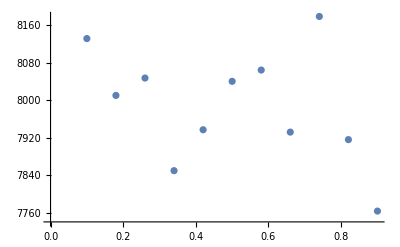

87869

```mathematica
vals=RandomReal[1,100000];
min=0.1;max=0.9;n=10;
Table[{δω,Tally[Sort[Chop[Abs[vals-δω],(max-min)/n/2]]][[1,2]]},{δω,min,max,(max-min)/n}];
%//ListPlot
%%[[All,2]]//Total
```

```mathematica
Table[{ky,kz,Total[Tally[Flatten[Table[Ε[0,ky+δky,kz+δkz,0,0,0]-ω,{δky,0,0.1,0.05},{δkz,0,0.1,0.05}]]][[All,2]]]},{ky,-4,4,0.1},{kz,-4,4,0.1}]
```

{{{-4.,-4.,36},{-4.,-3.9,36},{-4.,-3.8,36},{-4.,-3.7,36},{-4.,-3.6,36},{-4.,-3.5,36},{-4.,-3.4,36},{-4.,-3.3,36},{-4.,-3.2,36},63,{-4.,3.2,36},{-4.,3.3,36},{-4.,3.4,36},{-4.,3.5,36},{-4.,3.6,36},{-4.,3.7,36},{-4.,3.8,36},{-4.,3.9,36},{-4.,4.,36}},79,{1}}
 |  |  |  |

```mathematica
Manipulate[Plot3D[Ε[kx,ky,kz,m,b,0],{ky,-4,4},{kz,-4,4},PlotRange->{-2,2},MaxRecursion->4],{m,0,1},{b,0,5},{{kx,0},-5,5}]
```